```mathematica
f[x_]:=x^3+2x+1
```

```mathematica
x0=0;
```

```mathematica
x1=x0-f[x0]/f'[x0]
```

-1/2

```mathematica
x2=x1-f[x1]/f'[x1]
```

-5/11

```mathematica
x1=x0-f[x0]/f'[x0]//N
```

-0.5

```mathematica
x2=x1-f[x1]/f'[x1]//N
```

-0.454545

```mathematica
x3=x2-f[x2]/f'[x2]
```

-0.453398

```mathematica
x4=x3-f[x3]/f'[x3]
```

-0.453398

```mathematica
Solve[x^3+2x+1==0,x]//N
```

{{x→-0.453398},{x→0.226699+1.46771 ⅈ},{x→0.226699-1.46771 ⅈ}}

```mathematica
Err=Abs[x4-(-0.4533)]
```

0.0000976515

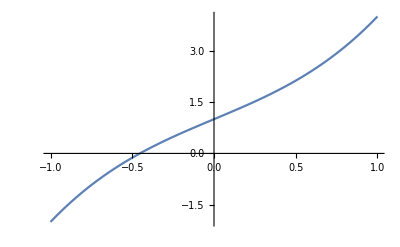

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
Plot[x^3+2x+1,{x,-1,1}]
```

-Graphics-

```mathematica
Bisection
f[x_]=x^3+2x+1
f[-1]->-2
f[0]->1
Iteration 1
a=-1;b=0;
x1=(a+b)/2//N
```

Bisection

1+2 x+x^3

-2→-2

1→1

Iteration

-0.5

```mathematica
f[-0.5]
```

-0.125

```mathematica
a=-0.5;b=0;
```

```mathematica
x3=(a+b)/2//N
```

-0.25

```mathematica
f[-0.25]
```

0.484375

```mathematica
a=-0.5;b=-0.25;
```

```mathematica
x4=(a+b)/2//N
```

-0.375

```mathematica
f[-0.375]
```

0.197266

```mathematica
x5=(a+b)/2//N
```

-0.4375

```mathematica
f[-0.4375]
```

0.0412598

```mathematica
x6=(a+b)/2//N
```

-0.3125

```mathematica
f[-0.3125]
```

0.344482

```mathematica
(22/7)//N[10]
```

```mathematica
10.[22/7]
regular falsi vala
```

10.[22/7]

falsi regular vala

```mathematica
f[x_]:=x^3-2x-5
```

```mathematica
Solve[f[x]==0]//N
```

{{x→2.09455},{x→-1.04728+1.13594 ⅈ},{x→-1.04728-1.13594 ⅈ}}

```mathematica
f[1.5]
```

-4.625

```mathematica
f[2.5]
```

5.625

```mathematica
a=1.5; b=2.5;
```

```mathematica
x1=(a f[b]- f[a]b)/(f[b]-f[a])//N
```

(-1. (-5.-2. a+a^3) b+a (-5.-2. b+b^3))/(2. a-1. a^3-2. b+b^3)

```mathematica
x1=(a F[b]-F[a]b)/(b-a)//N
```

1. (-2.5 F[1.5]+1.5 F[2.5])

```mathematica
f[x_]:=x^3-2x-5
```

```mathematica
a=1.5; b=2.5;
```

```mathematica
f[a]
```

-4.625

```mathematica
f[b]
```

5.625

```mathematica
x1=(a f[b]-f[a] b)/(f[b]-f[a])//N
```

1.95122

```mathematica
f[x1]
```

-1.47364

```mathematica
a=x1; b=2.5;
```

```mathematica
x2=(a f[b]-f[a] b)/(f[b]-f[a])//N
```

2.06514

```mathematica
f[x2]
```

-0.322825

```mathematica
a=x2; b=2.5
```

2.5

```mathematica
x3=(a f[b]-f[a] b)/(f[b]-f[a])//N
```

2.08875

```mathematica
f[x3]
```

-0.0645863

```mathematica
a=x3; b=2.5
```

2.5

```mathematica
x4=(a f[b]-f[a] b)/(f[b]-f[a])//N
```

2.09341

```mathematica
f[x4]
```

-0.0126835

```mathematica
a=x4; b=2.5;
```

```mathematica
x5=(a f[b]-f[a] b)/(f[b]-f[a])//N
```

2.09433

```mathematica
f[x5]
```

-0.00248167

```mathematica
a=x5; b=2.5;
```

```mathematica
x6=(a f[b]-f[a] b)/(f[b]-f[a])//N
```

2.09451

```mathematica
f[x6]
```

-0.000485217

```mathematica
x7=(a f[b]-f[a] b)/(f[b]-f[a])//N
```

2.09451